```mathematica
eq1=C1*s*Vc[s]-C1*v0[t]-Vo[s]*Ra/(R2*(Ra+Rb))==0;
```

```mathematica
eq2=Vc[s]-Vo[s]+C1*(R1+R2)*(s*Vc[s]-v0[t])+L1*C1*(s^2*Vc[s]-s*v0[t])==0;
```

```mathematica
sol1=Solve[{eq1,eq2},{Vo[s],v0[t]}]
```

{{Vo[s]→(R2 (Ra+Rb) Vc[s])/(-R1 Ra+R2 Rb-L1 Ra s),v0[t]→-(-Ra Vc[s]-C1 R1 Ra s Vc[s]+C1 R2 Rb s Vc[s]-C1 L1 Ra s^2 Vc[s])/(C1 (R1 Ra-R2 Rb+L1 Ra s))}}

```mathematica
H[s]=Cancel[Extract[sol1,{1,1,2}]/Extract[sol1,{1,2,2}]]
```

(C1 R2 (Ra+Rb))/(-Ra-C1 R1 Ra s+C1 R2 Rb s-C1 L1 Ra s^2)

Si se cumple que R1=R2*Rb/Ra entonces ξ=0

```mathematica
Ho[s]=Cancel[H[s]/. {R1-> (R2*Rb)/Ra}]
```

-(C1 R2 (Ra+Rb))/(Ra (1+C1 L1 s^2))

```mathematica
polos=TransferFunctionPoles[TransferFunctionModel[Ho[s],s]]
```

{{{-ⅈ/(√C1 √L1),ⅈ/(√C1 √L1)}}}

```mathematica
InverseLaplaceTransform[Ho[s],s,t]/.Ra->Rb
```

-(2 √C1 R2 Sin[t/(√C1 √L1)])/(√L1)

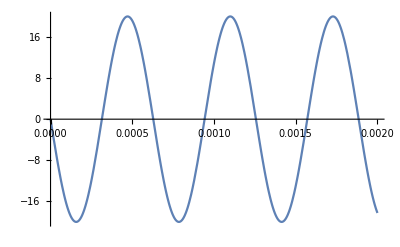

```mathematica
Plot[%/.{C1->1*10^-6,L1->10*10^-3,R2->1000},{t,0,0.002}]
```